```mathematica
ClearAll["Global`*"]
imax = 100;jmax = 100;w = 1.5;
r0 = 1;rmax = 2;Δr = (rmax - r0)/imax;
Δθ = 2*Pi/jmax;
u[0][i_,j_]:=0;
u[n_][0,j_]:=1;
u[n_][imax,j_]:=2;
u[n_][i_,-1]:=u[n-1][i,jmax-1];
For[n=1,n<1000,n++,Do[r=r0+i*Δr;u[n][i,j]=w/2*(r^2 Δr^2 Δθ^2)/(r^2 Δθ^2+Δr^2)*((u[n-1][i+1,j]+u[n][i-1,j])/Δr^2+(u[n-1][i+1,j]-u[n][i-1,j])/(2r Δθ)+(u[n-1][i,j+1]+u[n][i,j-1])/(r^2 Δθ^2))+(1-w)u[n-1][i,j];If[j==0,u[n][i,jmax]=u[n][i,0]];If[n>2,u[n-2][i,j]=.],{i,1,imax-1},{j,0,jmax-1}]]
```

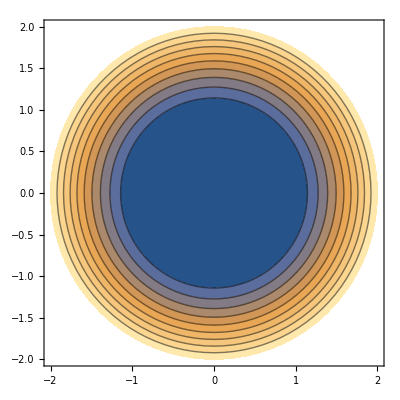

```mathematica
ListContourPlot[Flatten[Table[{x=(r0+i Δr )Cos[j Δθ],y=(r0+i Δr )Sin[j Δθ],u[n-1][i,j]},{i,0,imax},{j,0,jmax}],1]]
```